initial P = 150, initial Q (MT) = 100

```mathematica
demand[P_,ϵdemand_,initialP_,initialQ_]:=Module[{q,A},A=a/.Flatten[NSolve[initialQ==a initialP^ϵdemand,WorkingPrecision->30]];q=A P^ϵdemand;Return[q]];supply[P_,ϵsupply_,initialP_,initialQ_]:=Module[{q,A},A=a/.Flatten[NSolve[initialQ==a initialP^ϵsupply,WorkingPrecision->30]];q=A P^ϵsupply;Return[q]];ReboundRatio[initialP_,initialQ_,wasteavoided_,lossavoided_,ϵsupply_,ϵdemand_]:=Module[{supply1,supply2,demand1,demand2,Q2,P2,reboundratio},supply1=supply[p,ϵsupply,initialP,initialQ];demand1=demand[p,ϵdemand,initialP,initialQ];supply2=supply1+lossavoided;demand2=demand1-wasteavoided;P2=p/.Flatten[NSolve[demand2==supply2,WorkingPrecision->30]];Q2 = demand2/.p->P2;reboundratio=((Q2-initialQ)+wasteavoided)/(wasteavoided+lossavoided);Return[reboundratio]];
```

```mathematica
demand[p,-0.5,150,100]
```

1224.74487139158895044130576217/p^0.5

```mathematica
supply[p,0.5,150,100]
```

8.16496580927726052138925237357 p^0.5

```mathematica
ReboundRatio[150,100,10,10,0.4,-0.6]
```

0.623326

```mathematica
data=Partition[Flatten[Table[{ϵsupply,ϵdemand,100*ReboundRatio[150,100,10,10,ϵsupply,ϵdemand]},{ϵsupply,0.25,0.7,0.05},{ϵdemand,-1.1,-0.3,0.1}]],3];
```

```mathematica
<<ColorBrewer`
```

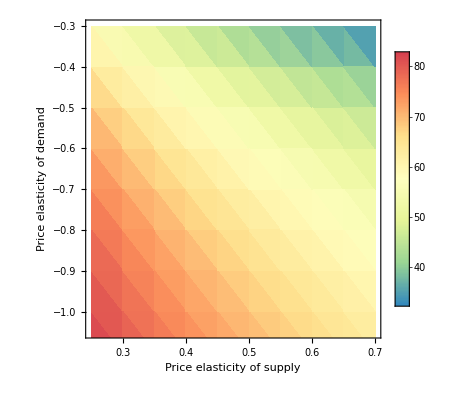

```mathematica
Fig3bottom=ListDensityPlot[data,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],ColorFunction->CreateColorFunction[Spectral,7,True],PlotLegends->Automatic,PlotRange->{{0.25,0.7},{-1.05,-0.3},{30,90}}]
```

```mathematica
Module[{directory=SystemDialogInput["Directory"]},If[directory=!=$Canceled,SetDirectory[directory]]] (*generates a dialog box allowing you to set the working directory. Set it where the data file "Hfoodwaste-fig4b.csv" is saved*)
```

/Users/mburgess/Desktop/Hegwood-food-waste

```mathematica
foodtype= Transpose[Delete[ Import["foodwaste-fig4b.csv","Table","FieldSeparators"->{","}],1]]⟦1⟧;incomegroup= Transpose[Delete[ Import["foodwaste-fig4b.csv","Table","FieldSeparators"->{","}],1]]⟦2⟧;supplyelasticites= Transpose[Delete[ Import["foodwaste-fig4b.csv","Table","FieldSeparators"->{","}],1]]⟦3⟧;demandelasticites= Transpose[Delete[ Import["foodwaste-fig4b.csv","Table","FieldSeparators"->{","}],1]]⟦4⟧;demandelasticitytype= Transpose[Delete[ Import["foodwaste-fig4b.csv","Table","FieldSeparators"->{","}],1]]⟦6⟧;data2=Transpose[{foodtype,incomegroup,supplyelasticites,demandelasticites,demandelasticitytype}];dataraw=Transpose[{supplyelasticites,demandelasticites}];
```

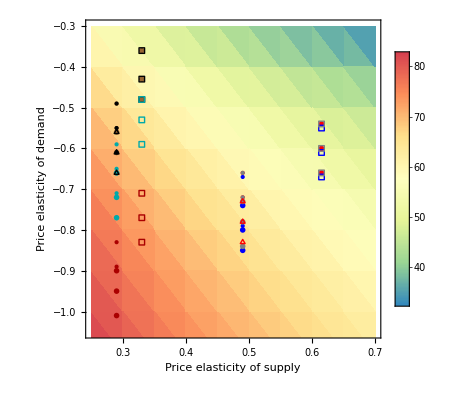

```mathematica
Fig3=Show[Fig3bottom,
ListPlot[{dataraw⟦1⟧,dataraw⟦22⟧,dataraw⟦43⟧},PlotMarkers->▵,PlotStyle->Directive[Brown,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Cereals, Low income*),
ListPlot[{dataraw⟦8⟧,dataraw⟦29⟧,dataraw⟦50⟧},PlotStyle->Directive[Brown,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Cereals, Middle income*),
ListPlot[{dataraw⟦15⟧,dataraw⟦36⟧,dataraw⟦57⟧},PlotMarkers->▢,PlotStyle->Directive[Brown,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Cereals, High income*),ListPlot[{dataraw⟦2⟧,dataraw⟦23⟧,dataraw⟦44⟧},PlotMarkers->△,PlotStyle->Directive[Black,PointSize[Medium]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Roots & tubers, Low income*),
ListPlot[{dataraw⟦9⟧,dataraw⟦30⟧,dataraw⟦51⟧},PlotStyle->Directive[Black,PointSize[Medium]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Roots & tubers, Middle income*),
ListPlot[{dataraw⟦16⟧,dataraw⟦37⟧,dataraw⟦58⟧},PlotMarkers->□,PlotStyle->Directive[Black,PointSize[Medium]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Roots & tubers, High income*),ListPlot[{dataraw⟦3⟧,dataraw⟦24⟧,dataraw⟦45⟧},PlotMarkers->▵,PlotStyle->Directive[Darker[Red],PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Oilseeds & pulses, Low income*),
ListPlot[{dataraw⟦10⟧,dataraw⟦31⟧,dataraw⟦52⟧},PlotStyle->Directive[Darker[Red],PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Oilseeds & pulses, Middle income*),
ListPlot[{dataraw⟦17⟧,dataraw⟦38⟧,dataraw⟦59⟧},PlotMarkers->□,PlotStyle->Directive[Darker[Red],PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Oilseeds & pulses, High income*),ListPlot[{dataraw⟦4⟧,dataraw⟦25⟧,dataraw⟦46⟧},PlotMarkers->▵,PlotStyle->Directive[Darker[Cyan],PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Fruits & vegetables, Low income*),
ListPlot[{dataraw⟦11⟧,dataraw⟦32⟧,dataraw⟦53⟧},PlotStyle->Directive[Darker[Cyan],PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Fruits & vegetables, Middle income*),
ListPlot[{dataraw⟦18⟧,dataraw⟦39⟧,dataraw⟦60⟧},PlotMarkers->□,PlotStyle->Directive[Darker[Cyan],PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Fruits & vegetables, High income*),ListPlot[{dataraw⟦5⟧,dataraw⟦26⟧,dataraw⟦47⟧},PlotMarkers->△,PlotStyle->Directive[Red,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Meat, Low income*),
ListPlot[{dataraw⟦12⟧,dataraw⟦33⟧,dataraw⟦54⟧},PlotStyle->Directive[Red,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Meat, Middle income*),
ListPlot[{dataraw⟦19⟧,dataraw⟦40⟧,dataraw⟦61⟧},PlotMarkers->▢,PlotStyle->Directive[Red,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Meat, High income*),ListPlot[{dataraw⟦6⟧,dataraw⟦27⟧,dataraw⟦48⟧},PlotMarkers->▵,PlotStyle->Directive[Blue,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Fish & seafood, Low income*),
ListPlot[{dataraw⟦13⟧,dataraw⟦34⟧,dataraw⟦55⟧},PlotStyle->Directive[Blue,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Fish & seafood, Middle income*),
ListPlot[{dataraw⟦20⟧,dataraw⟦41⟧,dataraw⟦62⟧},PlotMarkers->□,PlotStyle->Directive[Blue,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Fish & seafood, High income*),ListPlot[{dataraw⟦7⟧,dataraw⟦28⟧,dataraw⟦49⟧},PlotMarkers->▵,PlotStyle->Directive[Gray,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Milk, Low income*),
ListPlot[{dataraw⟦14⟧,dataraw⟦35⟧,dataraw⟦56⟧},PlotStyle->Directive[Gray,PointSize[Medium]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Milk, Middle income*),
ListPlot[{dataraw⟦21⟧,dataraw⟦42⟧,dataraw⟦63⟧},PlotMarkers->□,PlotStyle->Directive[Gray,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Milk, High income*)
]
```

```mathematica
Export["hegwood-foodwaste-fig4b.svg", %]
```

filename.svg